# The Model File of exotic decaying H

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=SetDirectory["C:\\Users\\Zhen\\Documents\\GitHub\\feynrules-current"]
<<FeynRules`
```

C:\Users\Zhen\Documents\GitHub\feynrules-current

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

## Load model

```mathematica
SetDirectory[NotebookDirectory[]];
LoadModel["SM.fr","H_exotic.fr"]
(*LoadRestriction["Massless.rst","DiagonalCKM.rst"]*)
```

Merging model-files...

This model implementation was created by

Zhen, Liu

Model Version: 1.0

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model H_exotic_decay loaded.

## Check terms

```mathematica
FeynmanGauge=False;
CheckHermiticity[Lexo]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 8 cores

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

## Outputs and interfaces

### UFO output

```mathematica
FeynmanGauge=False;
WriteUFO[Lexo];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 8 cores

Collecting the different structures that enter the vertex.

43 possible non-zero vertices have been found -> starting the computation:  / 43.

38 vertices obtained.

Flavor expansion of the vertices:  / 38

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 51

Squared matrix elent compute in 0.953125 seconds.

/ 60

Decay widths computed in 0.296875 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 8 kernels.

- Optimizing: /82 .

- Writing files.

Done!

## Check Lagrangian

```mathematica
?Lexo
```

```mathematica
LH//TraditionalForm
```

-(A0^6 H K_A6)/(720 MA0^3)-(A0^5 H K_A5)/(120 MA0^2)-(A0^4 H K_A4)/(24 MA0)-1/6 A0^3 H K_A3-1/2 A0^2 H MA0 K_A2

```mathematica
LA//TraditionalForm
```

-A0 u^-.u K_j-A0 mu^-.mu K_mu-A0^2 MA0^2+(∂_mu (A0))^2

```mathematica
FeynmanRules[LH,SelectParticles->{{A0,A0,H}},FlavorExpand->True]//Simplify//TraditionalForm
FeynmanRules[LH,SelectParticles->{{A0,A0,A0, H}},FlavorExpand->True]//Simplify//TraditionalForm
FeynmanRules[LH,SelectParticles->{{A0,A0,A0, A0, H}},FlavorExpand->True]//Simplify//TraditionalForm
FeynmanRules[LH,SelectParticles->{{A0,A0,A0, A0, A0, H}},FlavorExpand->True]//Simplify//TraditionalForm
FeynmanRules[LH,SelectParticles->{{A0,A0,A0, A0, A0, A0, H}},FlavorExpand->True]//Simplify//TraditionalForm
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Selecting specified field content. Warning! Only mass eigenstates should be selected!

Neglecting all terms with more than 3 particles.

Neglecting all terms with less than 3 particles.

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((A0 | 1
A0 | 2
H | 3) | -ⅈ MA0 K_A2)

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((A0 | 1
A0 | 2
A0 | 3
H | 4) | -ⅈ K_A3)

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((A0 | 1
A0 | 2
A0 | 3
A0 | 4
H | 5) | -(ⅈ K_A4)/MA0)

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((A0 | 1
A0 | 2
A0 | 3
A0 | 4
A0 | 5
H | 6) | -(ⅈ K_A5)/MA0^2)

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((A0 | 1
A0 | 2
A0 | 3
A0 | 4
A0 | 5
A0 | 6
H | 7) | -(ⅈ K_A6)/MA0^3)

```mathematica
FeynmanRules[LA,SelectParticles->{{u,ubar,A0}},FlavorExpand->True]//Simplify//TraditionalForm
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((u^- | 1
u | 2
A0 | 3) | -ⅈ K_j δ_(m_1,m_2) δ_(s_1,s_2))

```mathematica
FeynmanRules[LA,SelectParticles->{{mu,mubar,A0}},FlavorExpand->True]//Simplify//TraditionalForm
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

((mu^- | 1
mu | 2
A0 | 3) | -ⅈ K_mu δ_(s_1,s_2))

#### Post MG5 generation and test on the branching Fraction Scalings

```mathematica
widthlist={{2, 1.10*10^-7},{3, 1.06*10^-7},{4, 3.26*10^-8},{5,1.99*10^-8},{6,3.18*10^-9}}
```

{{2,1.1×10^-7},{3,1.06×10^-7},{4,3.26×10^-8},{5,1.99×10^-8},{6,3.18×10^-9}}

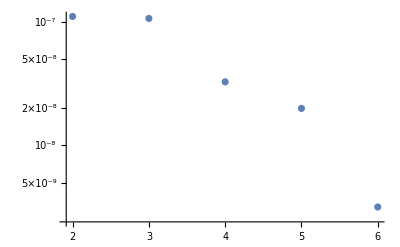

```mathematica
ListLogPlot[widthlist]
```

```mathematica
1/Sqrt[widthlist[[-1,2]]/widthlist[[1,2]]]^(1/4)
```

7.89643